```mathematica
ClearAll["Global`*"];
```

```mathematica
V[x_,y_,a_,e_]:=0.5*(-x^2/a^2-y^2/a^2)+(-1+e)/Sqrt[y^2/a^2+(x/a-e)^2]-e/Sqrt[y^2/a^2+(1+x/a-e)^2]
```

```mathematica
k=1;m=0.75;

grad[x_,y_] := Grad[V[x,y,k,m],{x,y}];
normal[x_,y_] = Simplify[grad[x,y]/(√(grad[x,y].grad[x,y]))];
deriv=D[V[x,0,k,m],x];
L1=FindRoot[deriv==0,{x,0}];
L2=FindRoot[deriv==0,{x,1.5}];
L3=FindRoot[deriv==0,{x,-1}];
L4=FindRoot[{D[V[x,y,k,m],x]==0,D[V[x,y,k,m],y]==0},{{x,0},{y,1}}];
L5=FindRoot[{D[V[x,y,k,m],x]==0,D[V[x,y,k,m],y]==0},{{x,0},{y,-1}}];
LP={{x/.L1,0},{x/.L2,0},{x/.L3,0},{x/.L4,y/.L4},{x/.L5,y/.L5}};
```

```mathematica
m2=1;
m1=m2*(1-m)/m;
μ1=m2/(m2+m1);
r[t_]:={x[t],y[t]};Manipulate[Show[Module[{orbita=NDSolve[{Thread[r''[t]=={2y'[t]+x[t]-(μ1 (x[t]+(1-μ1)))/(((x[t]+(1-μ1))^2+y[t]^2)^(3/2))-((1-μ1) (x[t]-μ1))/(((x[t]-μ1)^2+y[t]^2)^(3/2)),-2  x'[t]+y[t]-(μ1 y[t])/(((x[t]+(1-μ1))^2+y[t]^2)^(3/2))-((1-μ1) y[t])/(((x[t]-μ1)^2+y[t]^2)^(3/2))}],Thread[r'[0]=={vx0,vy0}],Thread[r[0]=={p[[1]],p[[2]]}]},r[t],{t,0,T}]}, ParametricPlot[r[t]/.orbita,{t,0,T},PlotRange->{{-1.5,1.5},{-1.5,1.5}}]],Graphics[{Darker[Yellow], PointSize[0.03], Point[{-m1/(m1+m2), 0}]}],Graphics[{Darker[Green], PointSize[0.02], Point[{m2/(m1+m2), 0}]}],
Graphics[{PointSize[0.02],Point[LP]}]
],{{T,50,"time"},0.0001,50,Appearance->"Labeled"},{{vx0,0,"vx_0"},-1.5,1.5,Appearance->"Labeled"},{{vy0,0.755,"vy_0"},-1.5,1.5,Appearance->"Labeled"},
{{p,{1,0}},Locator},
Button["L5",{p[[1]]=L5[[1]][[2]],p[[2]]=L5[[2]][[2]],vx0=0,vy0=0}],Button["L4",{p[[1]]=L4[[1]][[2]],p[[2]]=L4[[2]][[2]],vx0=0,vy0=0}],
Button["L3",{p[[1]]=L3[[1]][[2]],p[[2]]=0,vx0=0,vy0=0}],Button["L2",{p[[1]]=L2[[1]][[2]],p[[2]]=0,vx0=0,vy0=0}],Button["L1",{p[[1]]=L1[[1]][[2]],p[[2]]=0,vx0=0,vy0=0}]]
```

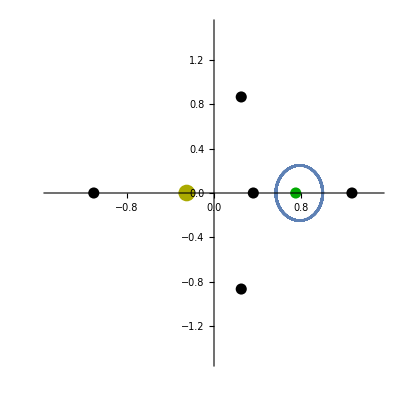

```mathematica
p={1,0};T=50;vx0=0;vy0=0.755;Show[Module[{orbita$=NDSolve[{Thread[r''[t]=={2 y'[t]+x[t]-(μ1 (x[t]+(1-μ1)))/(((x[t]+(1-μ1))^2+y[t]^2)^(3/2))-((1-μ1) (x[t]-μ1))/(((x[t]-μ1)^2+y[t]^2)^(3/2)),-2 x'[t]+y[t]-(μ1 y[t])/(((x[t]+(1-μ1))^2+y[t]^2)^(3/2))-((1-μ1) y[t])/(((x[t]-μ1)^2+y[t]^2)^(3/2))}],Thread[r'[0]=={vx0,vy0}],Thread[r[0]=={p⟦1⟧,p⟦2⟧}]},r[t],{t,0,T}]},ParametricPlot[r[t]/.orbita$,{t,0,T},PlotRange->{{-1.5,1.5},{-1.5,1.5}}]],Graphics[{Darker[Yellow],PointSize[0.03],Point[{-m1/(m1+m2),0}]}],Graphics[{Darker[Green],PointSize[0.02],Point[{m2/(m1+m2),0}]}],Graphics[{PointSize[0.02],Point[LP]}]]
```

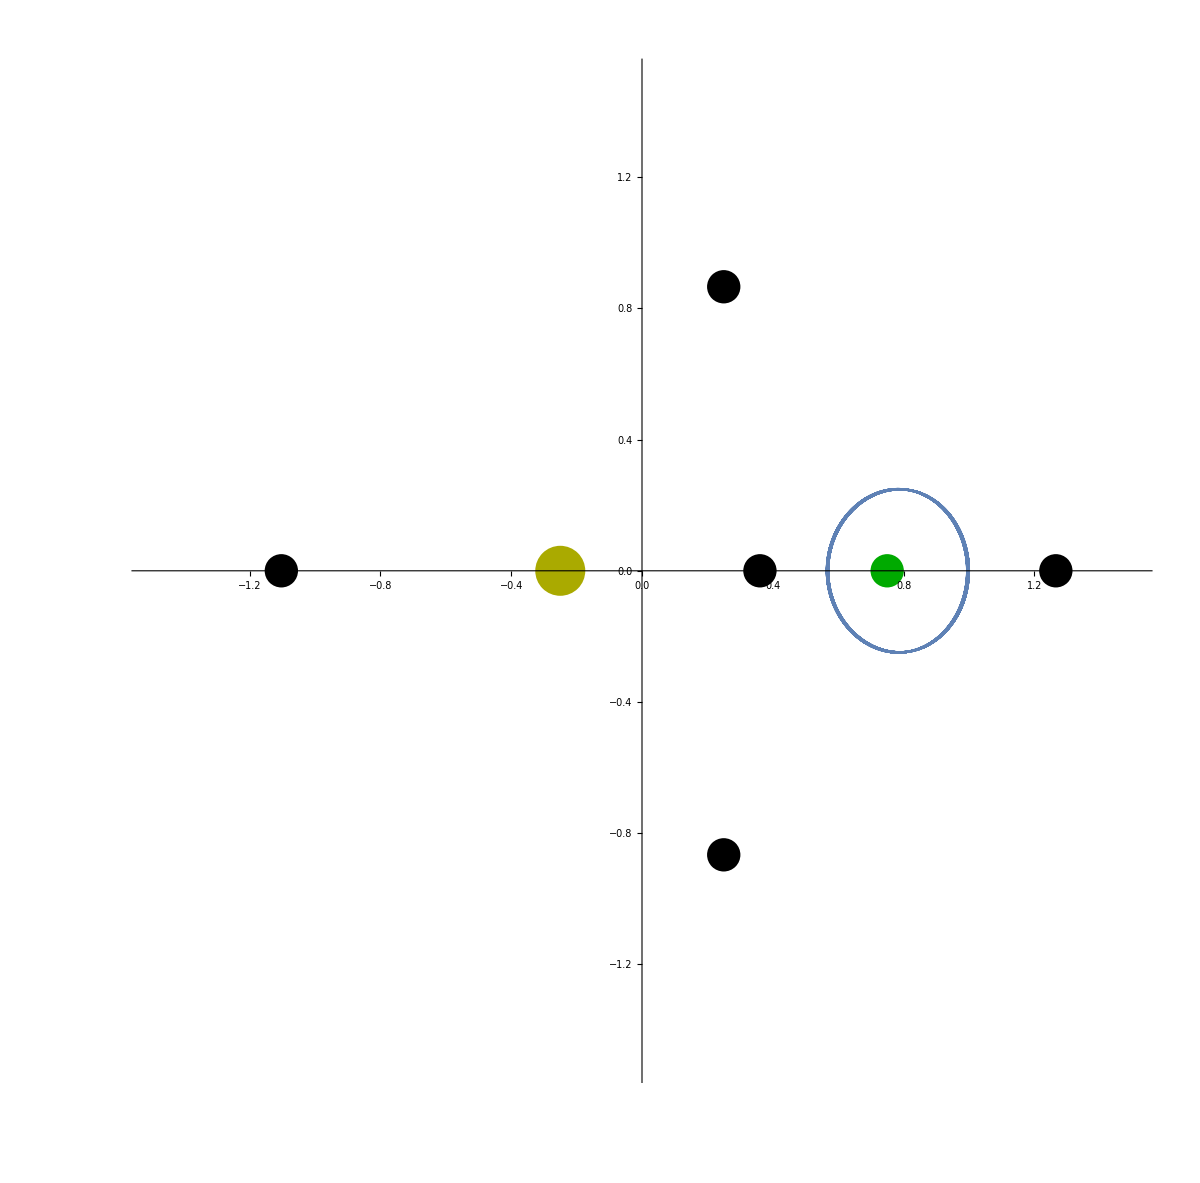

```mathematica
Show[%341,ImageSize->{1200,1183},AspectRatio->Full]
```

```mathematica
Export["C:\\Users\\Mike\\Documents\\Mana\\Trajectoria1.pdf",%342,"PDF"]
```

C:\Users\Mike\Documents\Mana\Trajectoria1.pdf